# Infra Bundles

We extract fibers, transport and global twisting from a graph and a vertex projection. The projection specifies observed positions; the vertices above each position are its internal states. We compare bundles over regular and irregular substrates, then follow a twisted covering through several resolutions.

## Setup

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

## Total space, projection and fibers

A fibered graph consists of a finite simple undirected unweighted untagged graph E and a map π on its vertices. The base graph B has vertex set π(V(E)). Two distinct base vertices are adjacent when a total edge joins their preimages. The fiber F_p is the induced graph on π^-1(p). Edges within a fiber are vertical; edges between fibers are transverse.

InfraFiberedGraph stores the total graph and projection. InfraTotalSpace, InfraBaseSpace and InfraProjection recover these data, and InfraFiber selects a fiber. The projection can be a function or an association.

The rows compare a square grid, a triangular tiling and an irregular square mesh. Every base point carries the same four-cycle of internal states. Each row shows the total graph with upright fibers on the left and its base on the right. The marked fiber projects to an intrinsically chosen graph centre. Here the product construction supplies the bundle. Each substrate uses the same four-cycle fiber and transports each internal state to the identically labeled state above every neighbour.

```mathematica
GraphicsGrid[ Map[ name |-> With[
  { base = BlockRandom[ InfraSubstrate[ name, "Medium", "KeepCoordinates" -> True ], RandomSeeding -> 2 ] },
  { fib = InfraFiberedGraph[ GraphProduct[ base, CycleGraph[ 4 ], "Cartesian" ], First ],
    point = First @ GraphCenter[ base ] },
  { Show[ InfraFiberedGraphHighlight[ fib, { InfraFiber[ fib, point ] }, Method -> "3DFiber", VertexLabels -> None ,
    "ThicknessRange" -> { 1.25, 5 } ], BoxRatios -> { 1, 1, .02 } ],
    InfraSubstrateHighlight[ base, { point }, VertexLabels -> None ,
      "ThicknessRange" -> { 1.25, 5 } ] } ],
  { "SquareGridGraph", "TriangularTilingGraph", "SquareMeshGraph" } ], ImageSize -> 1100 ]
```

-Graphics-

## When does the projection give a bundle?

For a total vertex x above p and a base neighbour q, the edge-lift multiplicity is

m(x,q)=|{y∈V(F_q):{x,y}∈E(E)}|.

InfraEdgeLiftMultiplicity records these counts, including zeros. Vertical neighbours do not enter the count.

Positive multiplicities give weak edge lifting, tested by InfraFibrationQ. Multiplicities at most one give InfraAtMostOneEdgeLiftQ, and multiplicities exactly one give InfraUniqueEdgeLiftingQ. A covering has unique lifts and edgeless fibers. A graph bundle has isomorphic fibers and unique lifts that preserve vertical adjacency.

Unique lifting makes the edges above each base edge a perfect matching. Every vertex on either side has exactly one partner, so fiber sizes match along the edge and hence throughout each connected base component. A covering over a connected base is therefore a bundle with a discrete fiber. Different base components may have different sheet counts.

Constancy of the multiplicities within each fiber is transverse equitability. Full equitability also requires constant vertical degree within each fiber.

The three pictures have the same two six-point fibers. On the left, one point in each fiber has no lift. In the middle, every point has several possible lifts. On the right, the transverse edges form a perfect matching. Equal fiber sizes alone do not distinguish these cases.

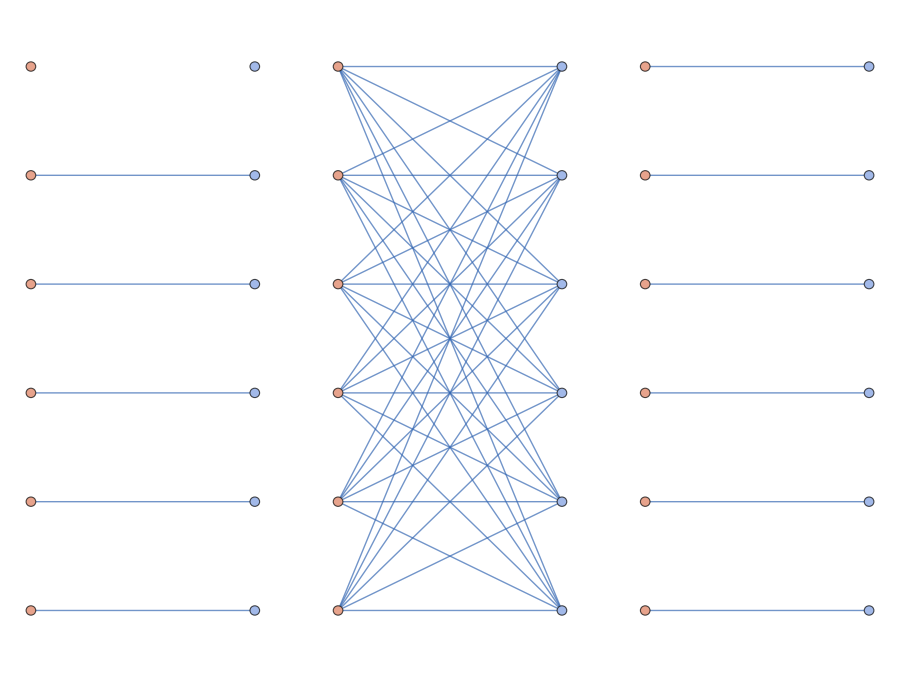

```mathematica
With[ { matching = UndirectedEdge @@@ Transpose[ { Range[ 6 ], Range[ 7, 12 ] } ],
    complete = UndirectedEdge @@@ Tuples[ { Range[ 6 ], Range[ 7, 12 ] } ],
    coordinates = Join[ Table[ { 0, index }, { index, 6 } ], Table[ { 2, index }, { index, 6 } ] ] },
  GraphicsRow[ Map[ edges |-> InfraFiberedGraphHighlight[
    InfraFiberedGraph[ Graph[ Range[ 12 ], edges ], vertex |-> Ceiling[ vertex / 6 ] ],
    Method -> "HighlightFiber", VertexCoordinates -> coordinates, VertexLabels -> None ,
    "ThicknessRange" -> { 1.25, 5 } ],
    { Most[ matching ], complete, matching } ], ImageSize -> 900 ] ]
```

For generated examples, RandomInfraFiberedGraph accepts explicit properties such as Properties -> { "FiberBundle" }. Its reference page gives the size and edge-count options.

## Connections and sections

A complete connection selects a perfect matching above every base edge, using transverse edges of the total graph. These matchings transport fiber vertices bijectively. InfraHorizontalLift composes them along a base walk from a chosen starting vertex, and InfraParallelTransport records all resulting endpoints. Preserving the vertical fiber graph is an additional requirement on the matchings. If the fibers are isomorphic and the matchings preserve adjacency, the vertical and selected transverse edges form a graph bundle.

Weak lifting does not ensure that such a connection exists. For two three-point fibers, take transverse edges x_1 y_1,x_2 y_1,x_3 y_2,x_3 y_3. Every endpoint has a neighbour, but x_1 and x_2 cannot both receive distinct partners. The left picture marks these two states in blue and their only possible partner in orange. On the right, adding the edge x_2 y_2 allows a complete matching, drawn in blue. The other available edges remain gray.

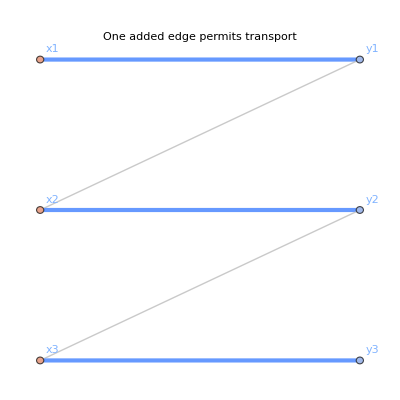

```mathematica
With[ { edges = UndirectedEdge @@@ { { 1, 4 }, { 2, 4 }, { 3, 5 }, { 3, 6 } },
    coordinates = { { 0, 2 }, { 0, 1 }, { 0, 0 }, { 2, 2 }, { 2, 1 }, { 2, 0 } },
    labels = Thread[ Range[ 6 ] -> { "x1", "x2", "x3", "y1", "y2", "y3" } ] },
  GraphicsRow[ {
    InfraFiberedGraphHighlight[
      InfraFiberedGraph[ Graph[ Range[ 6 ], edges ], vertex |-> Ceiling[ vertex / 3 ] ],
      { Style[ { 1, 2 }, StandardBlue ], Style[ 4, StandardOrange ] },
      Method -> "HighlightFiber", VertexCoordinates -> coordinates, VertexLabels -> labels,
      EdgeStyle -> GrayLevel[ .7 ], PlotLabel -> "Lifts exist, but no connection",
      "ThicknessRange" -> { 1.25, 5 } ],
    InfraFiberedGraphHighlight[
      InfraFiberedGraph[ Graph[ Range[ 6 ], Append[ edges, UndirectedEdge[ 2, 5 ] ] ],
        vertex |-> Ceiling[ vertex / 3 ] ],
      Style[ InfraConnection[ UndirectedEdge @@@ { { 1, 4 }, { 2, 5 }, { 3, 6 } } ],
        StandardBlue, AbsoluteThickness[ 3 ] ],
      Method -> "HighlightFiber", VertexCoordinates -> coordinates, VertexLabels -> labels,
      EdgeStyle -> GrayLevel[ .7 ], PlotLabel -> "One added edge permits transport",
      "ThicknessRange" -> { 1.25, 5 } ] }, ImageSize -> 900 ] ]
```

The obstruction concerns a set of states, not any single state: distinct partners for a set require at least as many neighbours as there are states in the set. Here two states have only one neighbour.

A section chooses one total vertex above each base vertex in its domain. It is continuous when adjacent base vertices receive adjacent choices. RandomInfraSection samples or extends sections; use Properties -> { "Continuous" } to require this condition. RandomInfraConnection samples complete connections.

The same three substrates distinguish selecting a state from transporting states. On the left, a continuous section selects one sheet of the product. On the right, the connection transports all four internal states along the base edges. The product labels make both constructions possible on the irregular mesh as well as on the regular grids.

```mathematica
GraphicsGrid[ Map[ name |-> With[
  { base = BlockRandom[ InfraSubstrate[ name, "Medium", "KeepCoordinates" -> True ], RandomSeeding -> 2 ] },
  { fib = InfraFiberedGraph[ GraphProduct[ base, CycleGraph[ 4 ], "Cartesian" ], First ] },
  { section = InfraSection[ AssociationMap[ point |-> { point, 1 }, VertexList[ base ] ] ],
    connection = InfraConnection[ Select[ EdgeList[ InfraTotalSpace[ fib ] ],
      edge |-> First[ First[ edge ] ] =!= First[ Last[ edge ] ] ] ] },
  { Show[ InfraFiberedGraphHighlight[ fib, Style[ section, StandardBlue, AbsoluteThickness[ 2.5 ] ],
      Method -> "3DFiber", VertexLabels -> None, EdgeStyle -> GrayLevel[ .7 ] ,
    "ThicknessRange" -> { 1.25, 5 } ], BoxRatios -> { 1, 1, .02 } ],
    Show[ InfraFiberedGraphHighlight[ fib, Style[ connection, StandardOrange ],
      Method -> "3DFiber", VertexLabels -> None, EdgeStyle -> GrayLevel[ .7 ] ,
      "ThicknessRange" -> { 1.25, 5 } ], BoxRatios -> { 1, 1, .02 } ] } ],
  { "SquareGridGraph", "TriangularTilingGraph", "SquareMeshGraph" } ], ImageSize -> 1100 ]
```

-Graphics-

## Twisting and holonomy

The holonomy of a closed base walk is its transport permutation of the starting fiber. The product on the left and the twisted cover on the right have the same sixteen-cycle base and two-point fibers. The colored walks lift one base circuit from the two states above vertex 1. Below each covering, arrows run from a copy of the starting fiber on the left to its endpoint fiber on the right.

```mathematica
With[ { product = InfraFiberedGraph[
    GraphProduct[ CycleGraph[ 16 ], Graph[ { 1, 2 }, { } ], "Cartesian" ], First ],
    twisted = InfraFiberedGraph[ CycleGraph[ 32 ], vertex |-> Mod[ vertex, 16, 1 ] ] },
  GraphicsGrid[ Transpose[ Map[ fib |-> With[
    { connection = InfraConnection[ EdgeList[ InfraTotalSpace[ fib ] ] ],
      fiber = VertexList[ InfraFiber[ fib, 1 ] ], loop = Append[ Range[ 16 ], 1 ] },
    { lifts = Map[ start |-> InfraHorizontalLift[ fib, connection, start, loop ], fiber ],
      permutation = PermutationList[ InfraHolonomy[ fib, connection, loop ], 2 ] },
    { InfraFiberedGraphHighlight[ fib,
        MapThread[ { lift, color } |-> Style[ InfraWalk[ lift ], color ], { lifts, { StandardBlue, StandardOrange } } ],
        "BaseGraphLayout" -> "CircularEmbedding", VertexLabels -> None ,
      "ThicknessRange" -> { 1.25, 5 } ],
      Graph[ Tuples[ { { 0, 1 }, { 1, 2 } } ],
        MapThread[ { state, endpoint } |-> DirectedEdge[ { 0, state }, { 1, endpoint } ],
          { Range[ 2 ], permutation } ],
        VertexCoordinates -> { { 0, 1 }, { 0, 0 }, { 2, 1 }, { 2, 0 } },
        VertexStyle -> { { 0, 1 } -> StandardBlue, { 1, 1 } -> StandardBlue,
          { 0, 2 } -> StandardOrange, { 1, 2 } -> StandardOrange }, VertexLabels -> None, VertexSize -> .12 ] } ],
    { product, twisted } ] ], ImageSize -> 1000 ] ]
```

-Graphics-

In the product, each lift closes on its initial state. In the twisted cover, the lift from vertex 1 ends at vertex 17, and the other lift returns from 17 to 1. Thus one base circuit exchanges the two states. InfraHolonomy computes this transposition.

This exchange prevents a continuous section over the whole base: successive adjacency choices force a return to the other state. The product has two continuous sections, one on each horizontal cycle.

More generally, a covering of a connected base has a continuous section exactly when some state in one fiber is fixed by every closed-walk transport based there. A section supplies such a state because every lifted circuit must return to its chosen vertex. Conversely, transport a common fixed state to each base point along any path. Two paths give the same endpoint: following one and reversing the other gives a closed walk that fixes the starting state. For a base edge, choose the path to its second endpoint through its first endpoint. Its last lifted edge joins the chosen states, so these path-independent choices form a continuous section. Thus a nonidentity holonomy obstructs a section only when the holonomy permutations have no common fixed state.

InfraTrivialMonodromyQ tests whether every closed base walk has identity transport. Equivalently, each horizontal connected component contains at most one vertex above each base vertex. Two such vertices in one component give a lifted closed walk with different endpoints, and every such walk gives two such vertices.

## The same cover at coarser resolutions

Take the double cover C_128→C_64 and group consecutive vertices into blocks of size b==1,4,16. Apply the same blocking to the total and base cycles. Across the top row, the same lifted base circuit is drawn over progressively coarser bases. The bottom row draws each total cycle in its own layout, making the two endpoints of the lifted circuit visible.

```mathematica
With[ { total = CycleGraph[ 128 ] },
  GraphicsGrid[ Transpose[ Map[ block |-> With[
    { coarseTotal = InfraBaseSpace[ InfraFiberedGraph[ total, vertex |-> Ceiling[ vertex / block ] ] ],
      baseSize = 64 / block },
    { fib = InfraFiberedGraph[ coarseTotal, vertex |-> Mod[ vertex, baseSize, 1 ] ] },
    { connection = InfraConnection[ EdgeList[ coarseTotal ] ] },
    { lift = InfraHorizontalLift[ fib, connection, 1, Append[ Range[ baseSize ], 1 ] ] },
    { highlights = { Style[ InfraWalk[ lift ], StandardBlue, AbsoluteThickness[ 2.5 ] ],
        Style[ InfraFiber[ fib, 1 ], StandardOrange ] } },
    { InfraFiberedGraphHighlight[ fib, highlights, "BaseGraphLayout" -> "CircularEmbedding",
        VertexLabels -> None, EdgeStyle -> GrayLevel[ .7 ] ,
      "ThicknessRange" -> { 1.25, 5 } ],
      InfraSubstrateHighlight[ Graph[ coarseTotal, GraphLayout -> "CircularEmbedding",
        VertexStyle -> GrayLevel[ .7 ], EdgeStyle -> GrayLevel[ .7 ] ], highlights,
        VertexLabels -> None ,
        "ThicknessRange" -> { 1.25, 5 } ] } ], { 1, 4, 16 } ] ], ImageSize -> 1000 ] ]
```

-Graphics-

At every resolution the blue walk joins the two orange states in the starting fiber. The twist survives blocking. This follows from an exact rule, beyond these three illustrations. For b|n with n/b≥3, write π_n:C_(2n)→C_n for reduction of vertex labels modulo n, using labels 1,…,n. The block maps α_b(v)==⌈v/b⌉ and β_b(p)==⌈p/b⌉ satisfy

π_(n/b)◦α_b==β_b◦π_n.

Edges within a block collapse, and edges between successive blocks form the smaller cycles. A circuit of the smaller base still lifts through half its total cycle and exchanges the two states. Assigning each coarse edge b times the original length also keeps the base circumference fixed. Thus this family has an explicit renormalization rule preserving covering degree and monodromy.

## Scope and further examples

The bundle predicate uses the Cartesian graph-bundle convention: above a base edge the graph is the Cartesian product of that edge with the common fiber. This permits global twisting; see Algorithm for recognizing Cartesian graph bundles, Section 2. Topological bundles require local product charts, while the weak fibration predicate here asks only for edge lifts; see Hatcher, Algebraic Topology, Section 4.2, pp. 376–377. Curvature requires a specified family of faces or loops in addition to the graph.

Experimental Infra Bundles constructs direction fibers from geodesic rays and tests their emergence across observation scales. The exact blocking rule above concerns this cycle family; other observation rules need their own compatibility checks.

The original tutorial credits the broad object and separate predicates to the April 2026 Meeting 1 notes of Pavel Hajek, Ioana Milea and Stephen Wolfram, unpublished. It credits fiber automorphisms and permutation holonomy to Ioana Milea's one-page Fibered Graph Gauge Theory Basics.

Related Guides

InfraFiberBundlespaclet:WolframInstitute/InfraGeometry/guide/InfraFiberBundles

Related Tech Notes

ExperimentalInfraBundlespaclet:WolframInstitute/InfraGeometry/tutorial/ExperimentalInfraBundles

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/InfraBundles

### Keywords

fibered graph

graph bundle

covering

edge lifting

multiplicity

section

connection

holonomy